## previous

```mathematica
(test = Block[{mx, my,maxI,sx,sy,bx=100,by=1024},
ParallelTable[
sx=5.1;sy=5.1;
maxI = RandomReal[];
{mx,my}= {RandomReal[bx], RandomReal[by]};
Table[(maxI*Exp[-((x-mx)^2/(2 sx^2))-((y-my)^2/(2*sy^2))]),{x,1,100},{y,1,1024}],
{100}]
];)//AbsoluteTiming
```

{0.87393,Null}

```mathematica
ImageAdd[Image/@test]//ImageAdjust
```

## Gaussian Image and autocorrelations

```mathematica
ClearAll@gaussianImage;
Options[gaussianImage]={"intensity"-> "random"};
gaussianImage[pts:{{_Real,_Real}..},num_:50,boundX_Integer:100,boundY_Integer:1024,sX_:5.1,sY_:5.1,OptionsPattern[]]:=Block[{sx=sX,sy=sY,maxI,mx,my,func},
If[OptionValue["intensity"]==="random",func:=RandomReal[],func=OptionValue@"intensity"];
ParallelTable[
maxI=func;
{mx,my}={First@#,Last@#}&@pts[[i]];
Table[(maxI*Exp[-((x-mx)^2/(2 sx^2))-((y-my)^2/(2*sy^2))]),{x,1,boundX},{y,1,boundY}],{i,num}]
];
```

```mathematica
imageCorrelation[input_Image]:=ImageAdjust@ImageCorrelate[input,input,PerformanceGoal->"Quality"];

autoCorr2D[input:{{_?NumberQ,_?NumberQ}..}|_Image]:=Module[{mat},If[Head@input===Image,mat=ImageData@input];
ListCorrelate[mat,mat,{-1,1},0]];
```

### random gaussians

```mathematica
pts=Table[{RandomReal[50],20.*i},{i,100}];
test=gaussianImage[pts,100,50];
```

```mathematica
ImageAdd[Image/@test]
```

```mathematica
img=-Graphics-;
```

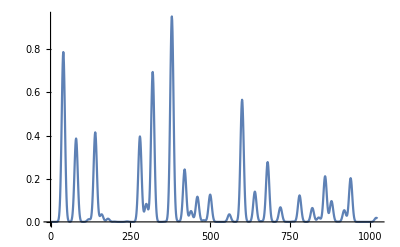

```mathematica
ImageData[img][[25]]//ListPlot[#,Joined->True,PlotRange->All]&
```

```mathematica
ImageAdjust@ImageCorrelate[#,#,PerformanceGoal->"Quality"]&[img]
```

-Graphics-

```mathematica
Reverse@ImageDimensions@img
```

{50,1024}

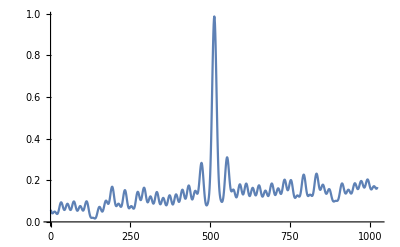

```mathematica
ImageData[-Graphics-][[25]]//ListPlot[#,Joined->True,PlotRange->All]&
```

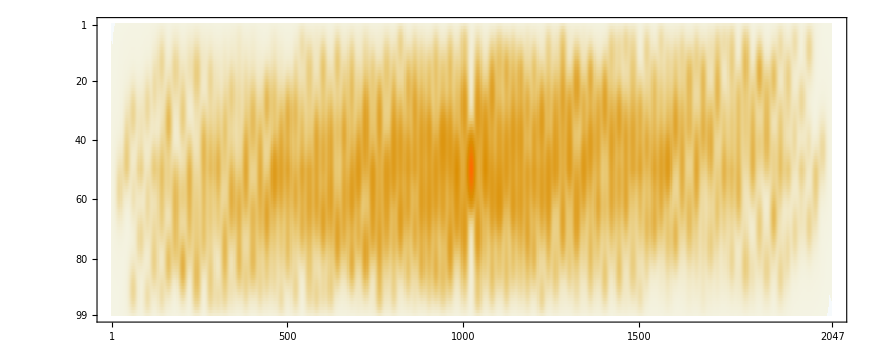

```mathematica
(corr=ListCorrelate[#,#,{-1,1},0]&[ImageData@img])//MatrixPlot
```

```mathematica
Dimensions@corr
```

{99,2047}

```mathematica
ListCorrelate[#,#,{-1,1},0]&[ImageData@img]//ArrayPlot[#,FrameTicks->True]&
```

-Graphics-

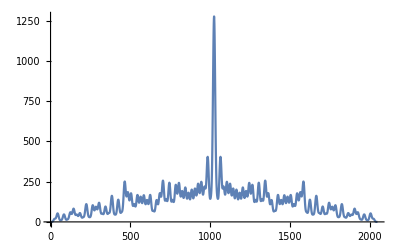

```mathematica
ListCorrelate[#,#,{-1,1},0][[50]]&[ImageData@img]//ListPlot[#,Joined->True,PlotRange->All]&
```

```mathematica
peaks=FindPeaks[corr[[50]],2];
```

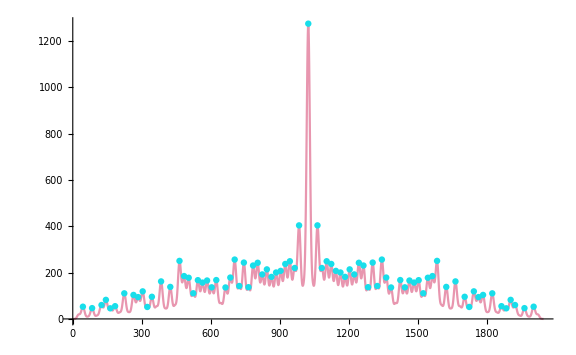

```mathematica
Show[ListPlot[corr[[50]],Joined->True,PlotStyle->RGBColor[0.9099728326945901, 0.5889291204377103, 0.6867986661568547],PlotRange->All],Graphics[{RGBColor[0.0921953942803575, 0.8688835926879261, 0.91625847306432],PointSize[0.008],Point@peaks}],ImageSize->Large]
```

```mathematica
N@*Mean@Differences@peaks[[All,1]]
```

24.5

```mathematica
Differences[ Map[First]@SortBy[TakeLargestBy[peaks,Last,3],First]]//Mean (* Distance to first lag *)
```

40

```mathematica
Differences[ Map[First]@Sort[TakeLargestBy[peaks,Last,3],First@#1≤ First@#2&]]//Mean (* Distance to first lag *)
```

40

### gaussians in line

```mathematica
pts=Table[{25.0,20.*i},{i,100}];
test=gaussianImage[pts,100,50];
```

```mathematica
ImageAdd[Image/@test]//ImageAdjust
```

```mathematica
img=-Graphics-;
```

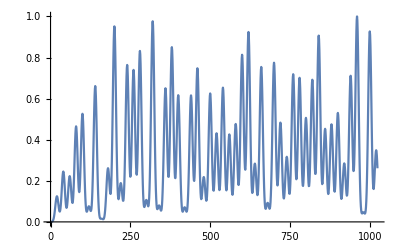

```mathematica
ImageData[img][[25]]//ListPlot[#,Joined->True,PlotRange->All]&
```

```mathematica
corr=ImageAdjust@ColorNegate@ImageCorrelate[#,#,NormalizedSquaredEuclideanDistance,PerformanceGoal->"Quality"]&[img]
```

-Graphics-

```mathematica
Reverse@ImageDimensions@corr
```

{50,1024}

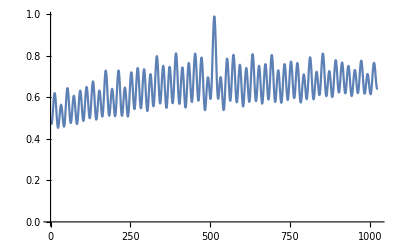

```mathematica
ImageData[-Graphics-][[25]]//ListPlot[#,Joined->True,PlotRange->All]&
```

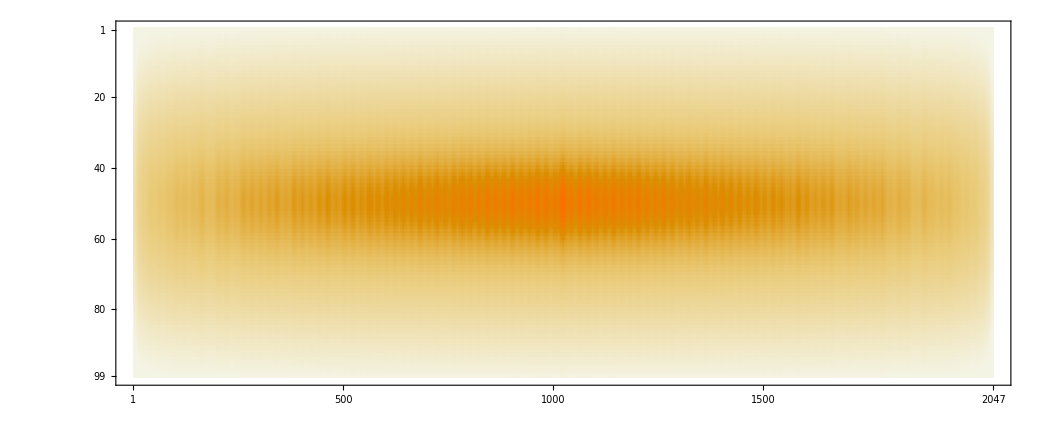

```mathematica
(corr=ListCorrelate[#,#,{-1,1},0]&[ImageData@img])//MatrixPlot
```

```mathematica
ListCorrelate[#,#,{-1,1},0]&[ImageData@img]//ArrayPlot[#,FrameTicks->True]&
```

-Graphics-

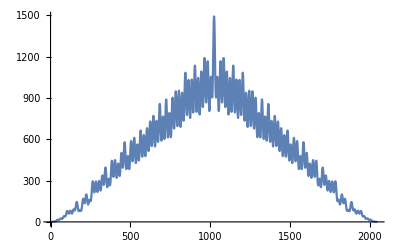

```mathematica
ListCorrelate[#,#,{-1,1},0][[50]]&[ImageData@img]//ListPlot[#,Joined->True,PlotRange->All]&
```

```mathematica
peaks=FindPeaks[corr[[50]],2,1,200]; (* taking all peaks above *)
```

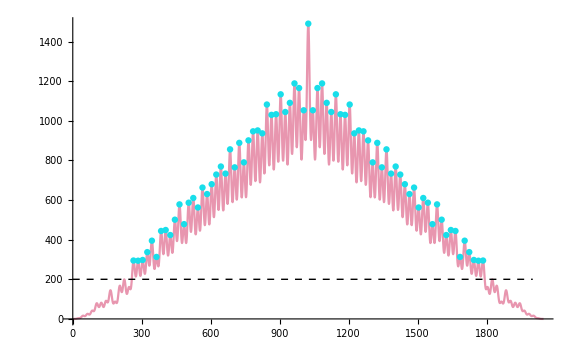

```mathematica
Show[ListPlot[corr[[50]],Joined->True,PlotStyle->RGBColor[0.9099728326945901, 0.5889291204377103, 0.6867986661568547],PlotRange->All],Graphics[{{RGBColor[0.0921953942803575, 0.8688835926879261, 0.91625847306432],PointSize[0.008],Point@peaks},{Dashed,Line[{{0,200},{2000,200}}]}}],ImageSize->Large]
```

```mathematica
N@*Mean@Differences@peaks[[All,1]]
```

20.

```mathematica
Differences[ Map[First]@Sort[TakeLargestBy[peaks,Last,20],First@#1≤ First@#2&]]//N@*Mean (* distance to first lag *)
```

21.0526

### gaussians in line

```mathematica
pts=Table[{25.0,20.*i},{i,50}];
test=gaussianImage[pts,50,50,1024,5.0,5.0,"intensity"-> 0.95];
```

```mathematica
ImageAdd[Image/@test]
```

```mathematica
img=-Graphics-;
```

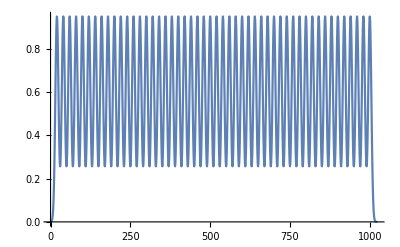

```mathematica
ImageData[img][[25]]//ListPlot[#,Joined->True]&
```

```mathematica
corr=ImageAdjust@ColorNegate@ImageCorrelate[#,#,NormalizedSquaredEuclideanDistance,PerformanceGoal->"Quality"]&[img]
```

-Graphics-

```mathematica
ImageDimensions@corr
```

{1024,50}

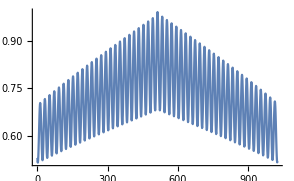

```mathematica
ImageData[-Graphics-][[25]]//ListPlot[#,Joined->True]&
```

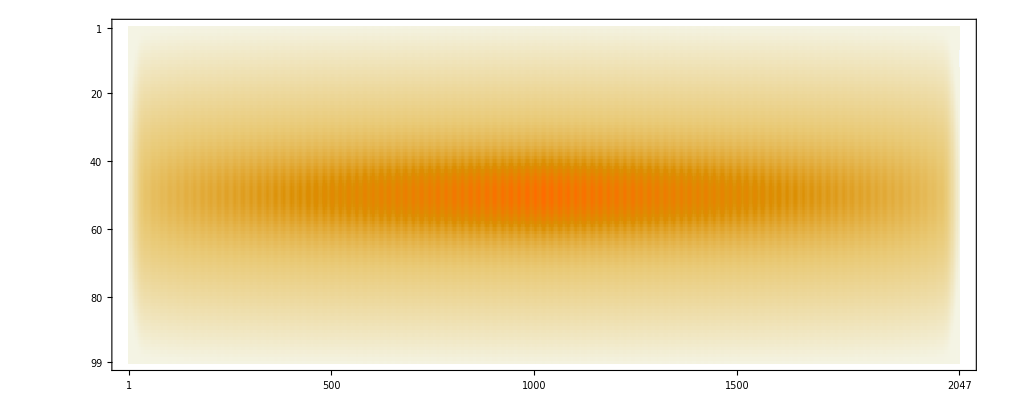

```mathematica
(corr=ListCorrelate[#,#,{-1,1},0]&[ImageData@img])//MatrixPlot
```

```mathematica
ListCorrelate[#,#,{-1,1},0]&[ImageData@img]//ArrayPlot[#,FrameTicks->True]&
```

-Graphics-

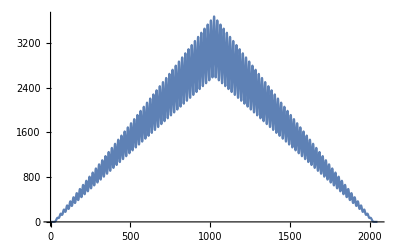

```mathematica
ListCorrelate[#,#,{-1,1},0][[50]]&[ImageData@img]//ListPlot[#,Joined->True,PlotRange->All]&
```

```mathematica
peaks=FindPeaks[corr[[50]],2,1,500];
```

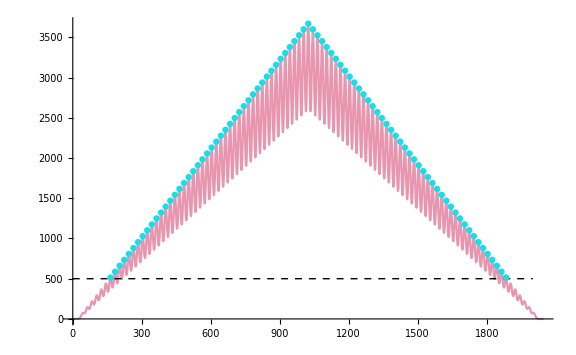

```mathematica
Show[ListPlot[corr[[50]],Joined->True,PlotStyle->RGBColor[0.9099728326945901, 0.5889291204377103, 0.6867986661568547]],Graphics[{{RGBColor[0.0921953942803575, 0.8688835926879261, 0.91625847306432],PointSize[0.008],Point@peaks},{Dashed,Line[{{0,500},{2000,500}}]}}],ImageSize->Large]
```

```mathematica
N@*Mean@Differences[peaks[[All,1]]]
```

20.

## image enlarged a bit

```mathematica
img=-Graphics-;
```

```mathematica
Reverse@ImageDimensions@img
```

{61,1247}

```mathematica
ImageAdjust@ImageCorrelate[img,img]
```

-Graphics-

```mathematica
corr=ListCorrelate[#,#,{-1,1},0]&[ImageData@img];
```

```mathematica
Dimensions@corr
```

{121,2493}

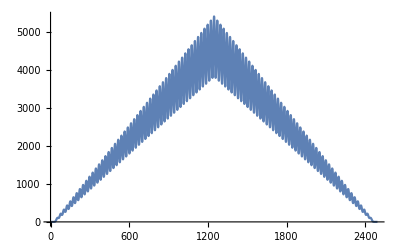

```mathematica
ListPlot[Part[corr,60],Joined->True]
```

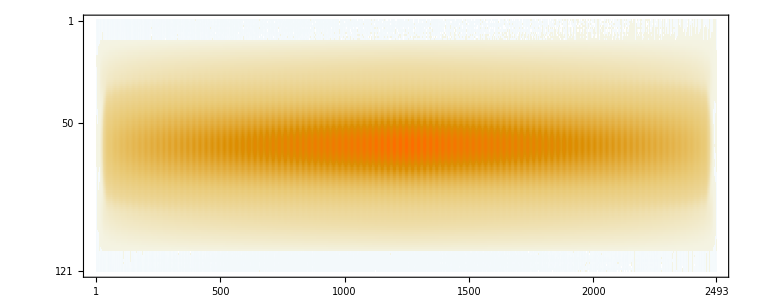

```mathematica
(corr=ListCorrelate[#,#,{-1,1},0]&[ImageData@img])//MatrixPlot
```

```mathematica
ArrayPlot[corr,ColorFunction->(ColorData["DarkRainbow"][#1]&), FrameTicks->True,ImageSize->Full]
```

-Graphics-

```mathematica
peaks=FindPeaks[corr[[60]],2,1,1000];
```

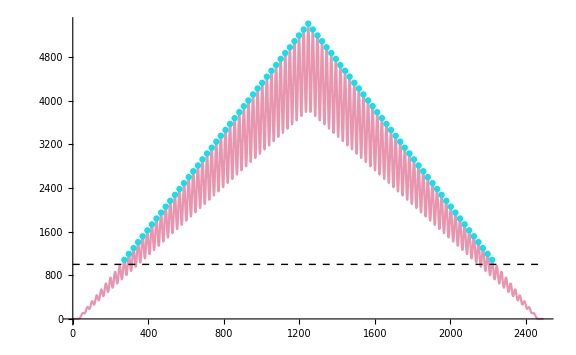

```mathematica
Show[ListPlot[corr[[60]],Joined->True,PlotStyle->RGBColor[0.9099728326945901, 0.5889291204377103, 0.6867986661568547]],Graphics[{{RGBColor[0.0921953942803575, 0.8688835926879261, 0.91625847306432],PointSize[0.008],Point@peaks},{Dashed,Line[{{0,1000},{2500,1000}}]}}],ImageSize->Large]
```

```mathematica
N@*Mean@Differences[peaks[[All,1]]]
```

24.35